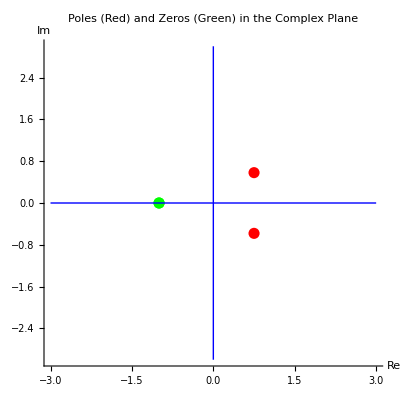

-Graphics3D-

```mathematica
(*Define the transfer function*)
transferFunction=(1+z)^2/(9/10-3/2 z+z^2);

(*Find poles and zeros*)
poles=Solve[Denominator[Together[transferFunction]]==0,z];
zeros=Solve[Numerator[Together[transferFunction]]==0,z];

(*Extract the values*)
poleValues=z/. poles;
zeroValues=z/. zeros;

(*Plotting*)
Graphics[{{Red,PointSize[0.02],Point[ReIm/@poleValues]},{Green,PointSize[0.02],Point[ReIm/@zeroValues]},{Blue,Thick,Line[{{-3,0},{3,0}}]},(*Real axis*){Blue,Thick,Line[{{0,-3},{0,3}}]}  (*Imaginary axis*)},Axes->True,AxesLabel->{"Re","Im"},PlotRange->{{-3,3},{-3,3}},PlotLabel->"Poles (Red) and Zeros (Green) in the Complex Plane"]
(*3D Complex Plot*)ComplexPlot3D[transferFunction,{z,-2-2 I,2+2 I},PlotRange->All,AxesLabel->{"Re","Im","Magnitude"},ColorFunction->"CyclicLogAbs",Mesh->None,Boxed->False,PlotLabel->"3D Complex Plot of the Transfer Function"]
```

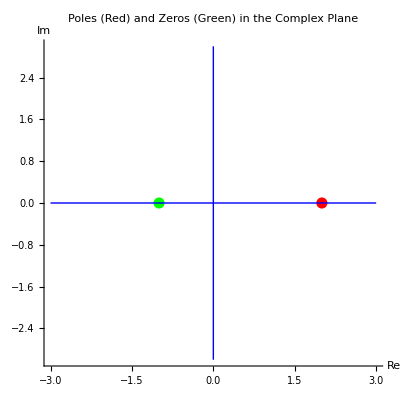

-Graphics3D-

```mathematica
(*Define the transfer function*)
transferFunction=(1+z)/(z-2);

(*Find poles and zeros*)
poles=Solve[Denominator[Together[transferFunction]]==0,z];
zeros=Solve[Numerator[Together[transferFunction]]==0,z];

(*Extract the values*)
poleValues=z/. poles;
zeroValues=z/. zeros;

(*Plotting*)
Graphics[{{Red,PointSize[0.02],Point[ReIm/@poleValues]},{Green,PointSize[0.02],Point[ReIm/@zeroValues]},{Blue,Thick,Line[{{-3,0},{3,0}}]},(*Real axis*){Blue,Thick,Line[{{0,-3},{0,3}}]}  (*Imaginary axis*)},Axes->True,AxesLabel->{"Re","Im"},PlotRange->{{-3,3},{-3,3}},PlotLabel->"Poles (Red) and Zeros (Green) in the Complex Plane"]
(*3D Complex Plot*)ComplexPlot3D[transferFunction,{z,-2-2 I,2+2 I},PlotRange->All,AxesLabel->{"Re","Im","Magnitude"},ColorFunction->"CyclicLogAbs",Mesh->None,Boxed->False,PlotLabel->"3D Complex Plot of the Transfer Function"]
```